# Visualization of the approximate mixture model

## Interface to the library

```mathematica
convert[inp_?StringQ]:=ToExpression@StringReplace[inp,"e"->"*10^"];
Map[convert,ReadList["!/Users/philipp/Source/tfbayes/libphylotree/phylotree-mathematica < /Users/philipp/Source/tfbayes/libphylotree/phylotree-parser-test2.nh",Record]];
```

## Visualization of the mixture model

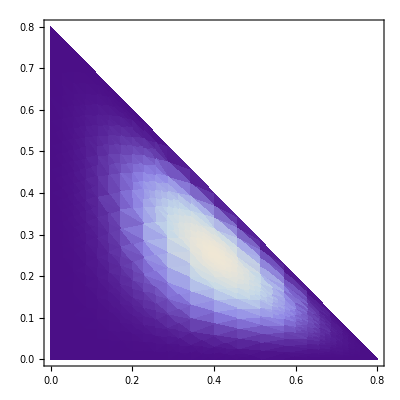

```mathematica
Pg=0.2;DensityPlot[100000000f[Pa,Pc,Pg,(1-Pa-Pc-Pg)],{Pa,0,1-Pg},{Pc,0,1-Pa-Pg}]
Remove[Pg];
```

## Visualization of the approximation

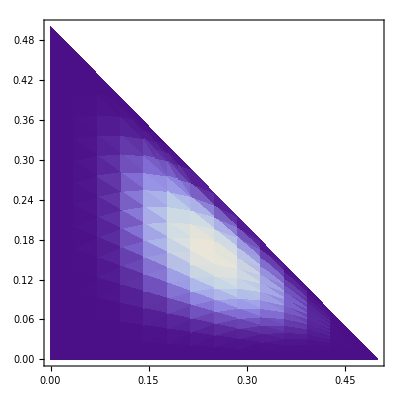

```mathematica
Pg=0.5;DensityPlot[g[Pa,Pc,Pg,(1-Pa-Pc-Pg)],{Pa,0,1-Pg},{Pc,0,1-Pa-Pg}]
Remove[Pg];
```

## Visual comparison of the four expectations

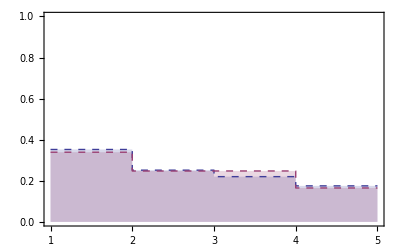

```mathematica
ListPlot[{Append[fxp,fxp[[4]]],Append[gxp,gxp[[4]]]},
InterpolationOrder->0,
PlotStyle->Dashed,
Joined->True,
Frame->True,
Filling->Axis,
PlotRange->{{1,5},{0,1}}]
```

## Simple example of the approximation

```mathematica
(* mixture weights *)
w={0.24433,0.3233,0.43237};
(* counts for each component *)
n1={3,4,5};
n2={2,7,4};
n3={4,4,5};
```

```mathematica
(* compute the first moment of the mixture model *)
w.Map[Moment[#,{1,0}]&,
{DirichletDistribution[n1],
DirichletDistribution[n2],
DirichletDistribution[n3]}]
```

0.243858

```mathematica
(* and the first moment of the approximation *)
Moment[DirichletDistribution[w.{n1,n2,n3}],{1,0}]
```

0.24374